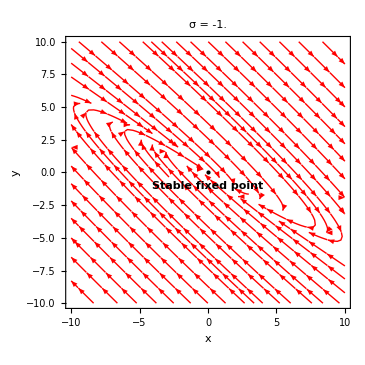

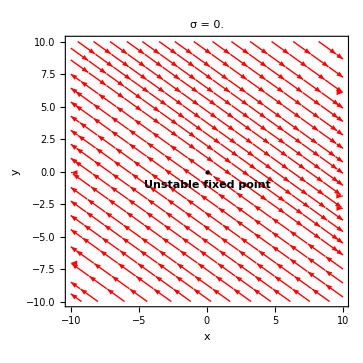

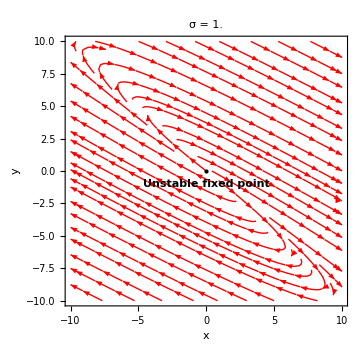

```mathematica
sigma0 = -1;
StreamPlot[
{(sigma +3)*x + 4y, -9/4 x + (sigma-3)y}/.{sigma->sigma0}, 
{x, -10,10}, 
{y, -10,10}, 
StreamStyle -> {Red},
PlotLabel -> StringJoin["σ =  ", ToString[N[sigma0]]], 
FrameLabel->{Style["x",Black,Medium],Style["y",Black,Medium]},
Epilog->{{PointSize[Large],Point[{0,0}]},Text[Style["Stable fixed point",Medium, Bold],{0,-1}]},
LabelStyle->Directive[FontSize->15]
]

sigma0 = 0;
StreamPlot[
{(sigma +3)*x + 4y, -9/4 x + (sigma-3)y}/.{sigma->sigma0}, 
{x, -10,10}, 
{y, -10,10}, 
StreamStyle -> {Red},
PlotLabel -> StringJoin["σ =  ", ToString[N[sigma0]]], 
FrameLabel->{Style["x",Black,Medium],Style["y",Black,Medium]},
Epilog->{{PointSize[Large],Point[{0,0}]},Text[Style["Unstable fixed point",Medium, Bold],{0,-1}]},
LabelStyle->Directive[FontSize->15]
]

sigma0 = 1;
StreamPlot[
{(sigma +3)*x + 4y, -9/4 x + (sigma-3)y}/.{sigma->sigma0}, 
{x, -10,10}, 
{y, -10,10}, 
StreamStyle -> {Red},
PlotLabel -> StringJoin["σ =  ", ToString[N[sigma0]]], 
FrameLabel->{Style["x",Black,Medium],Style["y",Black,Medium]},
Epilog->{{PointSize[Large],Point[{0,0}]},Text[Style["Unstable fixed point",Medium, Bold],{0,-1}]},
LabelStyle->Directive[FontSize->15]
]
```